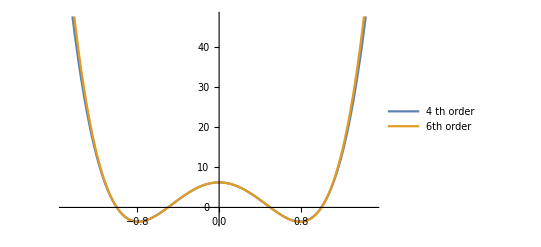

```mathematica
a=1;
b=0.5;
c = 5;
P4[x_]:=c^2(x^2-a^2)(x^2-b^2)
P6[x_]:=(x^2-a^2)(x^2-b^2)(x^2+c^2)
Plot[{P4[x],P6[x]},{x,-1.5,1.5}, PlotLegends->{"4 th order", "6th order"}]
```